{{2547,2537,2523,2607,2588,2504,2557,2484,2563,2543,2578,2523,2621,2650,2666,2569,2565,2568,2633,2678},{2548,2646,2608,2550,2575,2534,2595,2616,2611,2553,2650,2582,2673,2591,2611,2637,2631,2600,2531,2650},{2544,2651,2570,2559,2546,2582,2651,2679,2550,2439,2539,2568,2569,2487,2463,2545,2572,2548,2595,2694},{2542,2598,2532,2554,2662,2620,2641,2636,2589,2608,2590,2634,2586,2646,2595,2586,2641,2583,2563,2467}}

(2547 | 2537 | 2523 | 2607 | 2588 | 2504 | 2557 | 2484 | 2563 | 2543 | 2578 | 2523 | 2621 | 2650 | 2666 | 2569 | 2565 | 2568 | 2633 | 2678
2548 | 2646 | 2608 | 2550 | 2575 | 2534 | 2595 | 2616 | 2611 | 2553 | 2650 | 2582 | 2673 | 2591 | 2611 | 2637 | 2631 | 2600 | 2531 | 2650
2544 | 2651 | 2570 | 2559 | 2546 | 2582 | 2651 | 2679 | 2550 | 2439 | 2539 | 2568 | 2569 | 2487 | 2463 | 2545 | 2572 | 2548 | 2595 | 2694
2542 | 2598 | 2532 | 2554 | 2662 | 2620 | 2641 | 2636 | 2589 | 2608 | 2590 | 2634 | 2586 | 2646 | 2595 | 2586 | 2641 | 2583 | 2563 | 2467)

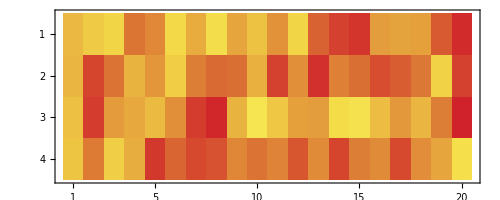

-Graphics3D-

```mathematica
dane = Import["E:\\Gry\\Moje dokumenty\\Dropbox\\test.txt"]//ToExpression
dane//MatrixForm
MatrixPlot[dane,ColorFunction->"TemperatureMap"]
ListPlot3D[dane, ColorFunction->"TemperatureMap", Filling->Bottom, FillingStyle->Opacity[1]]
```

```mathematica
,
```

```mathematica
ListPlot3D[dane,Mesh->None, InterpolationOrder->1, ColorFunction->Function[{x,y,z},Hue[z]], Filling->Bottom, FillingStyle->Opacity[1]]
```

-Graphics3D-